```mathematica
SetDirectory["/users/ianmilligan1/"];
```

```mathematica
FileNames[]
```

{.bash_history,canadian-history-db2,cdnhistory_composition_spreadsheet.numbers,.CFUserTextEncoding,Desktop,dissertation-exports,Documents,Downloads,.dropbox,Dropbox,.DS_Store,Library,mallet-2.0.7,mallet-2.0.7.tar.gz,Movies,Music,Pictures,Public,sample-test,tmp,.Trash}

```mathematica
test=Import["cdnhistory_composition_spreadsheet.csv"];
```

```mathematica
test[[1]]
```

{31,0.241221,27,0.183339,8,0.172483,34,0.112381,7,0.0602744,1,0.0415628,44,0.0363503,17,0.0353418,13,0.0218916,15,0.0209752,4,0.0182433,33,0.0115084,14,0.00763151,39,0.00732908,28,0.00683709,45,0.00527339,38,0.00412589,21,0.00299729,35,0.00249851,37,0.00227297,29,0.00216654,20,0.00122035,11,0.000617,5,0.000385,30,0.000269,0,0.000261,3,0.00012,36,0.000117,18,0.0000505,6,0.0000413,24,0.0000363,2,0.0000272,16,0.0000217,40,0.0000182,23,0.0000167,41,0.0000163,10,0.0000132,9,0.0000108,49,8.26×10^-6,47,7.16×10^-6,32,6.79×10^-6,46,5.87×10^-6,26,5.51×10^-6,19,4.95×10^-6,12,4.77×10^-6,43,4.22×10^-6,48,3.3×10^-6,25,1.65×10^-6,22,9.18×10^-7,42,3.67×10^-7}

```mathematica
n97=test[[1]];
n98=test[[2]];
n99=test[[3]];
n00=test[[4]];
n01=test[[5]];
n02=test[[6]];
n03=test[[7]];
n04=test[[8]];
n05=test[[9]];
n06=test[[10]];
n07=test[[11]];
n08=test[[12]];
n09=test[[13]];
n10=test[[14]];
```

```mathematica
all={n97,n98,n99,n00,n01,n02,n03,n04,n05,n06,n07,n08,n09,n10};
```

```mathematica
Length[n97]
```

100

```mathematica
topics={};
tr=Range[1,50];
Do[
yearcount={};
x=1;
Do[
var=Take[input,{x,x+1}];
AppendTo[yearcount,var];
,{x,tr}];
AppendTo[topics,yearcount];
,{input,all}];
```

```mathematica
topics;
```

```mathematica
topics[[4]]
```

{{31,0.252319},{0.252319,41},{41,0.23179},{0.23179,8},{8,0.199755},{0.199755,7},{7,0.0608542},{0.0608542,15},{15,0.0521828},{0.0521828,49},{49,0.0382718},{0.0382718,34},{34,0.0337472},{0.0337472,44},{44,0.0288352},{0.0288352,1},{1,0.0284672},{0.0284672,38},{38,0.0191573},{0.0191573,22},{22,0.013937},{0.013937,33},{33,0.0136278},{0.0136278,17},{17,0.013327},{0.013327,4},{4,0.0069084},{0.0069084,21},{21,0.00679034},{0.00679034,27},{27,3.87×10^-6},{3.87×10^-6,37},{37,3.51×10^-6},{3.51×10^-6,16},{16,2.93×10^-6},{2.93×10^-6,26},{26,2.81×10^-6},{2.81×10^-6,3},{3,2.58×10^-6},{2.58×10^-6,36},{36,1.41×10^-6},{1.41×10^-6,6},{6,1.41×10^-6},{1.41×10^-6,10},{10,1.29×10^-6},{1.29×10^-6,9},{9,9.37×10^-7},{9.37×10^-7,25},{25,8.2×10^-7},{8.2×10^-7,20}}

```mathematica
Cases[topics[[1]],{31,_}]
```

{{31,0.241221}}

```mathematica
count31={};
Do[
output=Cases[topics[[x]],{31,_}];
AppendTo[count31,output];
,{x,Range[1,14]}];
```

```mathematica
count31
```

{{{31,0.241221}},{{31,0.164333}},{{31,0.172222}},{{31,0.252319}},{{31,0.188238}},{{31,0.183194}},{{31,0.209946}},{{31,0.183118}},{{31,0.180616}},{{31,0.144937}},{{31,0.172033}},{{31,0.218527}},{{31,0.218468}},{{31,0.24517}}}

```mathematica
Length[count31]
```

14

```mathematica
topiclist=Range[0,49];
```

```mathematica
y=34;
count34={};
Do[
output=Cases[topics[[x]],{y,_}];
AppendTo[count34,output];
,{x,Range[1,14]}];
```

```mathematica
count34
```

{{{34,0.112381}},{{34,0.229263}},{{34,0.202368}},{{34,0.0337472}},{{34,0.159531}},{{34,0.149786}},{{34,0.111278}},{{34,0.128304}},{{34,0.127413}},{{34,0.259359}},{{34,0.126318}},{{34,0.0646405}},{{34,0.0790042}},{{34,0.00730626}}}

```mathematica
count2={};
y=2;
Do[
output=Cases[topics[[x]],{y,_}];
AppendTo[count2,output];
,{x,Range[1,14]}];
count2
```

{{},{},{},{},{},{},{},{{2,0.199957}},{},{{2,0.00012}},{{2,0.000133}},{{2,2.55×10^-6}},{{2,0.000163}},{{2,0.000263}}}

```mathematica
count10={};
y=10;
Do[
output=Cases[topics[[x]],{y,_}];
AppendTo[count10,output];
,{x,Range[1,14]}];
```

```mathematica
count10
```

{{},{},{},{{10,1.29×10^-6}},{},{},{},{{10,0.000175}},{{10,0.194643}},{{10,0.0000743}},{{10,0.0000295}},{},{},{{10,0.000108}}}

```mathematica
count8={};
y=8;
Do[
output=Cases[topics[[x]],{y,_}];
AppendTo[count8,output];
,{x,Range[1,14]}];
count8
```

{{{8,0.172483}},{{8,0.1592}},{{8,0.149705}},{{8,0.199755}},{{8,0.168276}},{{8,0.169272}},{{8,0.185504}},{{8,0.19038}},{{8,0.168391}},{{8,0.14057}},{{8,0.175903}},{{8,0.205092}},{{8,0.182254}},{{8,0.224022}}}

```mathematica
count27={};
y=27;
Do[
output=Cases[topics[[x]],{y,_}];
AppendTo[count27,output];
,{x,Range[1,14]}];
count27
```

{{{27,0.183339}},{},{},{{27,3.87×10^-6}},{},{},{},{},{},{},{},{{27,1.77×10^-6}},{{27,0.0000289}},{{27,0.0000841}}}

```mathematica
count24={};
y=24;
Do[
output=Cases[topics[[x]],{y,_}];
AppendTo[count24,output];
,{x,Range[1,14]}];
count24
```

{{},{{24,0.172132}},{},{},{{24,0.000142}},{},{},{},{},{},{},{{24,7.75×10^-7}},{{24,0.000084}},{}}

```mathematica
count41={};
y=41;
Do[
output=Cases[topics[[x]],{y,_}];
AppendTo[count41,output];
,{x,Range[1,14]}];
count41
```

{{},{},{},{{41,0.23179}},{},{},{},{},{},{},{},{{41,3.32×10^-7}},{},{}}

```mathematica
count9={};
y=9;
Do[
output=Cases[topics[[x]],{y,_}];
AppendTo[count8,output];
,{x,Range[1,14]}];
count8
```

```mathematica
overallcount={};
Do[
count={};
Do[
output=Cases[topics[[x]],{y,_}];
AppendTo[count,output];
,{x,Range[1,14]}];
AppendTo[overallcount,count];
,{y,Range[0,49]}];
```

```mathematica
overallcount[[35]]
```

{{{34,0.112381}},{{34,0.229263}},{{34,0.202368}},{{34,0.0337472}},{{34,0.159531}},{{34,0.149786}},{{34,0.111278}},{{34,0.128304}},{{34,0.127413}},{{34,0.259359}},{{34,0.126318}},{{34,0.0646405}},{{34,0.0790042}},{{34,0.00730626}}}

```mathematica
graphlist={};
Do[
AppendTo[graphlist,overallcount[[y]]];
,{y,Range[1,49]}];
```

```mathematica
overallcount[[0]]
```

List

```mathematica
Length[overallcount]
```

50

```mathematica
overallcount[[0]]
```

List

```mathematica
graphlist[[1]]
```

{{},{{0,0.00342769}},{{0,0.00503465}},{},{{0,0.000187}},{},{},{},{},{},{},{},{},{}}

```mathematica
graphlist[[2]]
```

{{{1,0.0415628}},{{1,0.0545451}},{{1,0.0395874}},{{1,0.0284672}},{{1,0.0390904}},{{1,0.0344695}},{{1,0.0326128}},{{1,0.0380631}},{{1,0.03585}},{{1,0.0241216}},{{1,0.0421645}},{{1,0.0130107}},{{1,0.0249861}},{{1,0.00526902}}}

```mathematica
? Export
```

Export[file.ext,expr] exports data to a file, converting it to the format corresponding to the file extension ext. 
Export[file,expr,format] exports data in the specified format.
Export[file,exprs,elems] exports data by treating exprs as elements specified by elems.

```mathematica
Export["/users/ianmilligan1/test.xls",graphlist]
```

/users/ianmilligan1/test.xls

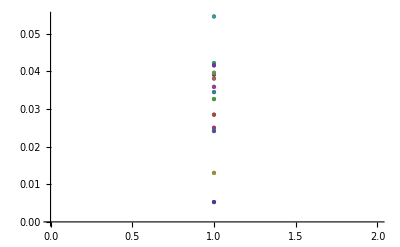

```mathematica
ListPlot[Reverse[graphlist[[2]]]]
```

```mathematica
test=graphlist[[34]][[All,1]][[All,2]]
```

{0.0115084,0.00539003,0.0158185,0.0136278,0.00756737,0.0017506,0.038599,0.00538894,0.00656522,0.00310004,0.00151645,7.75×10^-7,0.00205609,0.00125328}

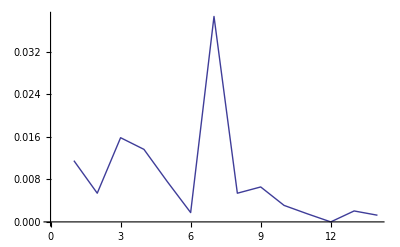

```mathematica
ListPlot[test,Joined->True]
```

```mathematica
test2=graphlist[[1]]
```

{{},{{0,0.00342769}},{{0,0.00503465}},{},{{0,0.000187}},{},{},{},{},{},{},{},{},{}}

```mathematica
graphlist[[1]]
```

{{},{{0,0.00342769}},{{0,0.00503465}},{},{{0,0.000187}},{},{},{},{},{},{},{},{},{}}

```mathematica
graphlist[[34]]
```

{{{33,0.0115084}},{{33,0.00539003}},{{33,0.0158185}},{{33,0.0136278}},{{33,0.00756737}},{{33,0.0017506}},{{33,0.038599}},{{33,0.00538894}},{{33,0.00656522}},{{33,0.00310004}},{{33,0.00151645}},{{33,7.75×10^-7}},{{33,0.00205609}},{{33,0.00125328}}}

```mathematica
graphlist[[1]][[All,1]]
```

Part::partw: Part 1 of {} does not exist.

{{},{{0,0.00342769}},{{0,0.00503465}},{},{{0,0.000187}},{},{},{},{},{},{},{},{},{}}⟦All,1⟧

```mathematica
mma={0,0.00342769,0.00503465,0,0.000187,0,0,0,0,0,0,0,0,0}
```

{0,0.00342769,0.00503465,0,0.000187,0,0,0,0,0,0,0,0,0}

```mathematica
Length[mma]
```

14

```mathematica
deletelist=graphlist/.{}->{{0,0}};
```

```mathematica
deletelist[[1]]
```

{0,{{0,0.00342769}},{{0,0.00503465}},0,{{0,0.000187}},0,0,0,0,0,0,0,0,0}

```mathematica
deletelist[[4]]
```

{0,{{3,0.00085}},{{3,0.00234341}},{{3,2.58×10^-6}},{{3,0.00113814}},{{3,0.000276}},{{3,0.00326227}},{{3,0.0136021}},{{3,0.0044252}},{{3,0.00166166}},{{3,0.000403}},0,{{3,0.128977}},{{3,0.00382966}}}

```mathematica
deletelist[[1]]
```

{{{0,0}},{{0,0.00342769}},{{0,0.00503465}},{{0,0}},{{0,0.000187}},{{0,0}},{{0,0}},{{0,0}},{{0,0}},{{0,0}},{{0,0}},{{0,0}},{{0,0}},{{0,0}}}

```mathematica
deletelist[[35]]
```

{{{34,0.112381}},{{34,0.229263}},{{34,0.202368}},{{34,0.0337472}},{{34,0.159531}},{{34,0.149786}},{{34,0.111278}},{{34,0.128304}},{{34,0.127413}},{{34,0.259359}},{{34,0.126318}},{{34,0.0646405}},{{34,0.0790042}},{{34,0.00730626}}}

```mathematica
deletelist[[1]][[All,1]][[All,2]]
```

{0,0.00342769,0.00503465,0,0.000187,0,0,0,0,0,0,0,0,0}

```mathematica
deletelist[[All,1,2]]
```

Part::partw: Part 2 of {{0, 0}} does not exist.

```mathematica
deletelist[[1]]
```

{{{0,0}},{{0,0.00342769}},{{0,0.00503465}},{{0,0}},{{0,0.000187}},{{0,0}},{{0,0}},{{0,0}},{{0,0}},{{0,0}},{{0,0}},{{0,0}},{{0,0}},{{0,0}}}

```mathematica
graphlist[[1]]
```

{{},{{0,0.00342769}},{{0,0.00503465}},{},{{0,0.000187}},{},{},{},{},{},{},{},{},{}}

```mathematica
If[#==={},0,#1[[1,2]]]&/@graphlist[[35]]
```

{0.112381,0.229263,0.202368,0.0337472,0.159531,0.149786,0.111278,0.128304,0.127413,0.259359,0.126318,0.0646405,0.0790042,0.00730626}

```mathematica
If[#==={},0,#1[[1,2]]]&/@graphlist[[1]]
```

{0,0.00342769,0.00503465,0,0.000187,0,0,0,0,0,0,0,0,0}

```mathematica
Manipulate[ListPlot[If[#==={},0,#1[[1,2]]]&/@graphlist[[x]],Joined->True,PlotRange->All],{x,35}]
```

Part::partd: Part specification graphlist ⟦ 35 ⟧ is longer than depth of object.

Part::partd: Part specification graphlist ⟦ 1, 2 ⟧ is longer than depth of object.

Part::partd: Part specification 35 ⟦ 1, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::pspec: Part specification 35 ⟦ 1, 2 ⟧ is neither a machine-sized integer nor a list of machine-sized integers.

ListPlot::lpn: graphlist ⟦ 1, 2 ⟧ ⟦ 35 ⟦ 1, 2 ⟧ ⟧ is not a list of numbers or pairs of numbers.

```mathematica
complist={};
Do[
results=If[#==={},0,#1[[1,2]]]&/@graphlist[[x]];
AppendTo[complist,results];
,{x,Range[1,49]}];
```

```mathematica
complist[[1]]
```

{0,0.00342769,0.00503465,0,0.000187,0,0,0,0,0,0,0,0,0}

```mathematica
complist
```

```mathematica
complist={{0,0.00342768669164354,0.00503464769633257,0,0.000187,0,0,0,0,0,0,0,0,0},{0.0415627991238424,0.0545451018506565,0.0395873926886832,0.0284671754269643,0.0390903566779343,0.0344695110117644,0.0326128167712641,0.0380630684019641,0.0358499768032886,0.0241216221583061,0.0421644617338612,0.013010650199335,0.0249861212092993,0.0052690153372215},{0,0,0,0,0,0,0,0.199956869995131,0,0.00012,0.000133,2.55*^-6,0.000163,0.000263},{0,0.00085,0.00234340543856465,2.58*^-6,0.00113813994196456,0.000276,0.00326226841883004,0.0136021043079029,0.00442520380663783,0.0016616611492715,0.000403,0,0.128977124171302,0.00382965986312563},{0.0182432511788783,0.0153210214876468,0.0161655849583081,0.00690840218135165,0.0157677946337962,0.0155492265181596,0.0244223588980269,0.0270170881666664,0.0225730014440221,0.0288058332884705,0.0295801137411838,0.061203806696065,0.0437452319638399,0.0507734401248714},{0.000385,0.000307,0,0,0,0.000336,0.00802923431352463,0.000139,0.000208,0,0,4.43*^-7,0,0},{0,0.000241,0,1.41*^-6,0,0,0,0,0,0.150548900654233,0.0000867,0,0.000224,0},{0.0602743718032286,0.0474997597520061,0.0564744169757092,0.060854234283426,0.0644049544569521,0.0677180178088576,0.0853233878689306,0.0668703874127514,0.0756713553056169,0.0537159237231518,0.0700926497509473,0.0781095052173989,0.081629734159972,0.117074442199532},{0.172483432576385,0.159200472513734,0.149704863560332,0.199755469922789,0.168275832383591,0.169271657972465,0.185503593663111,0.190379953106609,0.168390978281604,0.140569578751071,0.175902594476847,0.205091688988101,0.182253533569959,0.224022169891154},{0,0,0,9.37*^-7,0.173629161821008,0,0.000388,0,0,0,0.0000171,2.44*^-6,0.000155,0.000124},{0,0,0,1.29*^-6,0,0,0,0.000175,0.194643108706161,0.0000743,0.0000295,0,0,0.000108},{0.000617,0,0.00441197684714154,0,0,0.00118064355635489,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0.168560402389922,0,0,0,0.0000222,0,0.000111,0.0000723},{0.0218916444984702,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.00763151172418653,0.00602437173756045,0.00589922974900241,0,0.00287520906292886,0.00285523367406656,0.0020092736995706,0.00258591230554,0.00435057683917966,0.0173637765282861,0.00263044226375467,6.64*^-7,0.000613,0},{0.0209751877690279,0.016910560186972,0.021187508856956,0.0521827746960679,0.0215009564641114,0.02563297865619,0.0208108842627242,0.0240684726587026,0.0222189617576736,0.0183340496680296,0.0102658868690309,0.00894480817587124,0.0219672902273018,0.0172348504823046},{0,0,0,2.93*^-6,0.000153,0,0,0,0,0,0.0000718,0.189005866647421,0.000516,0.000133},{0.0353417572479726,0.0345687319967295,0.0370175036513323,0.0133269946190031,0.0435605127873028,0.052014138300888,0.0617327351560181,0.0569662195145231,0.0645225150340215,0.0643726893793305,0.0829366494245533,0.0686368194250108,0.0680453529033236,0.0227823454463182},{0,0.00130503156223181,0,0,0,0,0,0.00238305863478011,0.0040637598780872,0,0,0,0,0},{0,0,0.0307772761243821,0,0,0,0,0,0,0,0,0,0,0},{0.00122035187240515,0.0436412989311584,0.00898856782682784,0,0.00662467246969387,0.0526849927944909,0.00127172608719285,0.000388,0.00110225784572014,0.000818,0.0000486,2.88*^-6,0.0000275,0},{0.0029972943055629,0.00156144473437714,0.00381538978320398,0.0067903418701011,0.00245155731281088,0.00292331870982441,0.000222,0.000151,0.000595,0,0,0,0,0},{0,0,0,0.0139369728937976,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0.133026089393577,0,0,0,0,0,0,0,0},{0,0.172131500269011,0,0,0.000142,0,0,0,0,0,0,7.75*^-7,0.000084,0},{0,0,0,8.2*^-7,0,0,0,0,0.02797147340328,0,0,0,0,0},{0,0,0,2.81*^-6,0,0,0.00023,0,0,0,0,0,0.00213846794864907,0.244145022346169},{0.183338691870878,0,0,3.87*^-6,0,0,0,0,0,0,0,1.77*^-6,0.0000289,0.0000841},{0.00683709018198474,0.00212466184119373,0.00303001337112089,0,0.00968194514514483,0.00762741001694959,0.00250833085951056,0.0190875444699509,0.00304801475704441,0.00212888199717055,0.000945,0,0.000218,0.000899},{0.0021665374745286,0,0.00155612045682887,0,0,0.00117668293100609,0,0,0.00153365237823285,0,0,0,0,0},{0.000269,0,0,0,0.000362,0.000335,0.000494,0.00106692220215595,0.000442,0.000428,0.0000224,1.22*^-6,0,0.0312439576952032},{0.241221357515753,0.164333195316156,0.172221850227859,0.252319481040603,0.188238070179997,0.183194199079513,0.209946356372637,0.183117917559177,0.180615966702733,0.144936778682585,0.172033097052521,0.218526611551476,0.218468282933923,0.245169797239712},{0,0,0,0,0,0,0,0,0,0,0,0.0448793380686985,0,0},{0.0115083769356799,0.00539002784647049,0.0158185433764601,0.0136277673167128,0.00756737032281682,0.00175059640416711,0.0385989940251954,0.00538894306944245,0.00656522465152811,0.00310003768479449,0.00151644564122213,7.75*^-7,0.00205609061029669,0.00125328387494984},{0.112381378127771,0.229262807670723,0.202367548844671,0.0337472120256608,0.159530574471773,0.149786135661225,0.111278206806009,0.128303583209758,0.127412589510956,0.259358581851462,0.126318436289327,0.0646404903273539,0.0790041654280219,0.00730626079453828},{0.00249850988613475,0.00176835901589962,0.00184224685726173,0,0.0386793078402912,0.000707,0.000404,0.00019,0.000176,0.0000973,0,0,0,0.000147},{0,0,0,1.41*^-6,0,0,0,0,0,0.000139,0,0,0.106593171754363,0.000114},{0.0022729741791895,0.00251597063868508,0.00204169238596813,3.51*^-6,0.00136208400209557,0.00101316568446301,0.00463049449975122,0.00300588443466234,0.00660263555949669,0.00463831864038204,0.130109217789887,9.96*^-7,0.0203235638585545,0.00111894068258395},{0.00412589039808796,0.00266335247067469,0.0046085595213689,0.0191572765969209,0.0103551345622659,0.0178007477283456,0.00753134786408051,0.00631678359247348,0.00671467343492343,0.00536536158427935,0.050866451672414,5.53*^-7,0.00202624374857481,0.0214705532277773},{0.00732908467370177,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0.000274,0.159196498538115,0,0.000175,0,0.000169,0,0,0.000197,0,1.44*^-6,0,0},{0,0,0,0.231790104695369,0,0,0,0,0,0,0,3.32*^-7,0,0},{0,0,0,0,0,0,0,0,0,0,0.0804317091688308,0,0,0},{0,0,0,0,0.000273,0.00232318966887852,0.000385,0.00127250296466339,0.000703,0.000158,0.0000583,0.0214890133603179,0,0.000164},{0.0363503367804145,0.0331158726665565,0.0461689360885233,0.028835176913025,0.0434172273670112,0.039375405610471,0.0291833039958858,0.0286250234162782,0.0389971694361455,0.0238077881320256,0.0232466970354918,0.0264399276047229,0.0155432904851786,0.00496241152810234},{0.00527338818126831,0.000363,0.000937,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0.0363694795719432,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0.000316,0,0.0548132837576771,0,0,0,0},{0,0,0.00591068116691857,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
? AppendTo
```

AppendTo[s,elem] appends elem to the value of s, and resets s to the result.

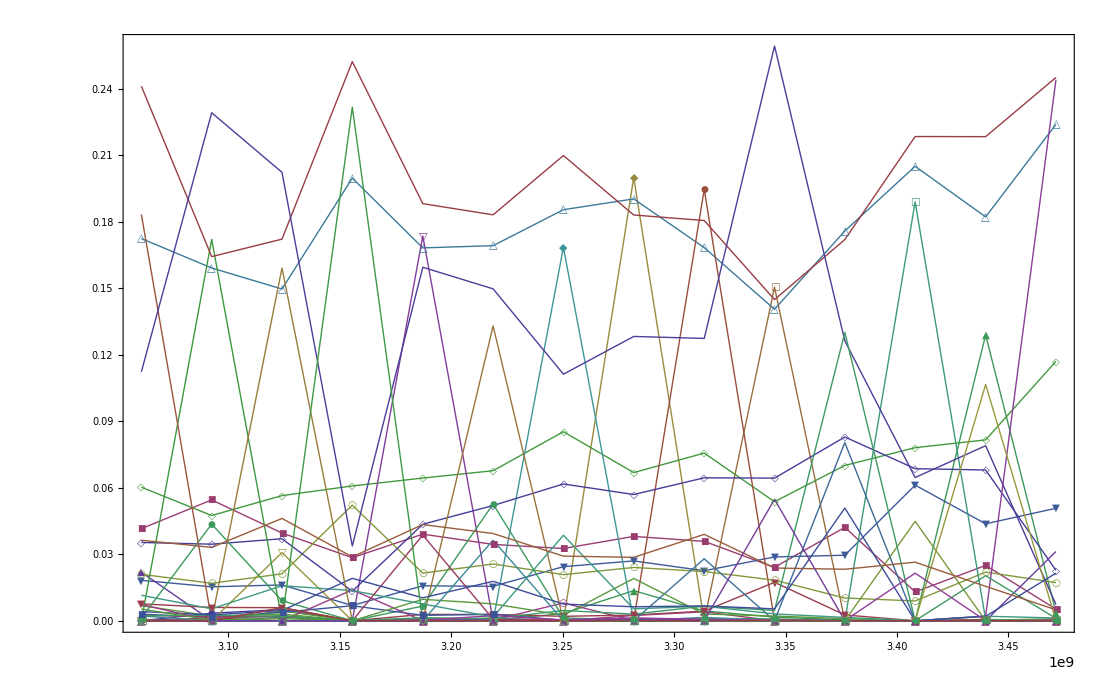

```mathematica
DateListPlot[complist,{1997},Joined->True,PlotRange->All,PlotMarkers->Automatic,PlotLabel->"Topics in Canadian History Dissertations, Top 50, 1997-2010"]
```

```mathematica
Manipulate[DateListPlot[complist[[x]],{1997},Joined->True,PlotRange->All,PlotMarkers->Automatic,Filling->Bottom,PlotLabel->{keys[[x]]}],{x,1,49,1}]
```

Part::partd: Part specification complist ⟦ 45 ⟧ is longer than depth of object.

Part::partd: Part specification keys ⟦ 45 ⟧ is longer than depth of object.

DateListPlot::ntdt: The first argument to DateListPlot should be a list of pairs of dates and real values, a list of real values, or a list of several such lists.

Part::partd: Part specification complist ⟦ 22 ⟧ is longer than depth of object.

Part::partd: Part specification keys ⟦ 22 ⟧ is longer than depth of object.

DateListPlot::ntdt: The first argument to DateListPlot should be a list of pairs of dates and real values, a list of real values, or a list of several such lists.

```mathematica
(** 2, 5, 8, 9, 16, 45 is key **)
```

```mathematica
keys=Import["/users/ianmilligan1/cdnhistory_keys.csv"];
```

```mathematica
topic2=complist[[2]]
```

{0.0415628,0.0545451,0.0395874,0.0284672,0.0390904,0.0344695,0.0326128,0.0380631,0.03585,0.0241216,0.0421645,0.0130107,0.0249861,0.00526902}

```mathematica
topic2="great toronto men faire opposition nac plans range";
```

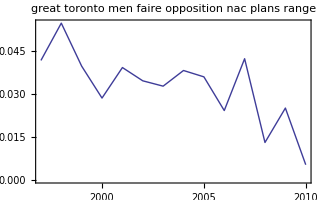

```mathematica
DateListPlot[complist[[2]],{1997},Joined->True,PlotLabel->"great toronto men faire opposition nac plans range"]
```

```mathematica
topic5="british toronto canada field fonds modern officers international james politics box chinese star jones space argues postwar centre election";
```

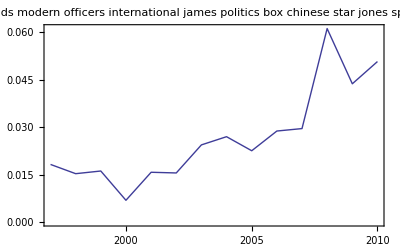

```mathematica
DateListPlot[complist[[5]],{1997},Joined->True,PlotLabel->"british toronto canada field fonds modern officers international james politics box chinese star jones space argues postwar centre election"]
```

```mathematica
topic8="toronto history time canada change years act west south western association archives community national immigrants women living press";
```

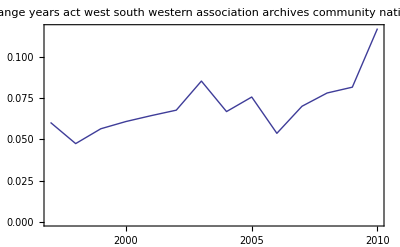

```mathematica
DateListPlot[complist[[8]],{1997},Joined->True,PlotLabel->"toronto history time canada change years act west south western association archives community national immigrants women living press"]
```

```mathematica
keys[[9]]
```

{8,permission canadian copyright reproduced ofthe reproduction canada prohibited owner press university war british social history north early land de }

```mathematica
topic9="canada owner press university war british social history north early land";
```

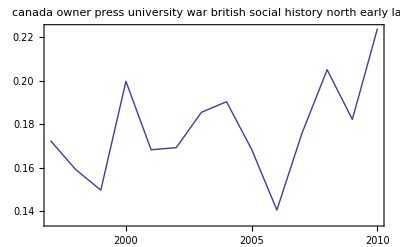

```mathematica
DateListPlot[complist[[9]],{1997},Joined->True,PlotLabel->"canada owner press university war british social history north early land"]
```

```mathematica
topic16="disease wife international simply required bay progress scientists cleark female provided relation site emigration";
```

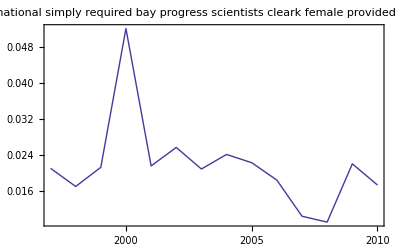

```mathematica
DateListPlot[complist[[16]],{1997},Joined->True,PlotRange->All,PlotLabel->"disease wife international simply required bay progress scientists cleark female provided relation site emigration"]
```

```mathematica
keys⟦45⟧
```

{44,permission prohibited copyright owner reproduction du reproduced le de economic dans east production nova saint canadians elle une wages }

```mathematica
topic45="economic east production nova saint canadians wages";
```

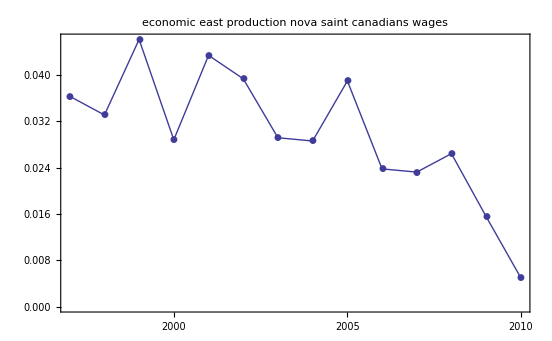

```mathematica
DateListPlot[complist[[45]],{1997},Joined->True,PlotMarkers->Automatic,PlotLabel->"economic east production nova saint canadians wages"]
```

```mathematica
complist[[45]]
```

{0.0363503,0.0331159,0.0461689,0.0288352,0.0434172,0.0393754,0.0291833,0.028625,0.0389972,0.0238078,0.0232467,0.0264399,0.0155433,0.00496241}

```mathematica
sparkline[data_]:=
DateListPlot[data,{1997},Axes->False,Frame->False,Joined->True,PlotRange->All,Filling->Bottom,AspectRatio->0.2,ImageSize->120]
```

```mathematica
Manipulate[sparkline[complist[[x]]],{x,1}]
```

Part::partd: Part specification complist ⟦ 16 ⟧ is longer than depth of object.

```mathematica
spark=sparkline[complist[[45]]]
```

-Graphics-

```mathematica
Grid[{{keys[[45]]},sparkline[complist[[45]]]}]
```

Grid[{{{44,permission prohibited copyright owner reproduction du reproduced le de economic dans east production nova saint canadians elle une wages }},-Graphics-}]

```mathematica
legend=keys[[45]];
```

```mathematica
Grid[{{a,b,c},{x,y,z}}]
```

a | b | c
1 | 41 | z

```mathematica
spark
```

-Graphics-

```mathematica
(** 2, 5, 8, 9, 16, 45 is key **)
```

```mathematica
complist[[29]]
```

{0.00683709,0.00212466,0.00303001,0,0.00968195,0.00762741,0.00250833,0.0190875,0.00304801,0.00212888,0.000945,0,0.000218,0.000899}

```mathematica
topic34="religious irish missionaries music policy church methodist police labor welfare trade executive";
```

```mathematica
keys[[29]]
```

{28,bureau baptiste pp francais paper tile companies preservation trading pulp universities managers valley ouvrage southem beaver ch revue usage }

```mathematica
keys[[22]]
```

{21,shortly lhe deletion fth tind witl dib endings govemrnent amounted diicult ymca volutionnaire heure emergent enally uni quartier gidney }

```mathematica
keys[[34]]
```

{33,permission religious nac irish reproduced prohibited copyright missionaries music policy church methodist police la labor welfare trade bom executive }

```mathematica
keys[[31]]
```

{30,net hay persons operational funher cleaning guiding jr gn regiment migration paint settlers latin emigration carter printing township myers }

```mathematica
complist[[31]]
```

{0.000269,0,0,0,0.000362,0.000335,0.000494,0.00106692,0.000442,0.000428,0.0000224,1.22×10^-6,0,0.031244}

```mathematica
Grid[{{"Mallet Topic Models, Cdn History Dissertations 1997-2010","Sparkline"},{topic2,sparkline[complist[[2]]]},{topic5,sparkline[complist[[5]]]},{topic8,sparkline[complist[[8]]]},{topic9,sparkline[complist[[9]]]},{topic16,sparkline[complist[[16]]]},{topic18,sparkline[complist[[18]]]},{topic22,sparkline[complist[[22]]]},{topic29,sparkline[complist[[29]]]},{topic31,sparkline[complist[[31]]]},{topic34,sparkline[complist[[34]]]},{topic45,sparkline[complist[[45]]]}},Frame->All,Background->{None,{LightGray}}]
```

Mallet Topic Models, Cdn History Dissertations 1997-2010 | Sparkline
great toronto men faire opposition nac plans range | -Graphics-
british toronto canada field fonds modern officers international james politics box chinese star jones space argues postwar centre election | -Graphics-
toronto history time canada change years act west south western association archives community national immigrants women living press | -Graphics-
canada owner press university war british social history north early land | -Graphics-
disease wife international simply required bay progress scientists cleark female provided relation site emigration | -Graphics-
canada history cultural university british canadians world aboriginal | -Graphics-
deletion endings government ymca emergent | -Graphics-
bureau francais paper tile companies preservation trading pulp universities managers valley ourage beaver usage | -Graphics-
persons operational cleaning guiding regiment migration paint settlers latin emigration carter printing township | -Graphics-
religious irish missionaries music policy church methodist police labor welfare trade executive | -Graphics-
economic east production nova saint canadians wages | -Graphics-